```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.3,Jtwo,2*0.3,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.5}]
```

{z→0.5}

```mathematica
Clear[IntPlus,NullsHolm,G,P,Inv]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.3,l->2*0.3}
```

0.5+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
p= Check[FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
],z->0];
AppendTo[lst,{Jtwoo,p}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.5]]
```

{{0.005,0.506138},{0.01,0.512055},{0.015,0.51775},{0.02,0.523225},{0.025,0.528481},{0.03,0.533517},{0.035,0.538333},{0.04,0.542928},{0.045,0.547302},{0.05,0.551452},{0.055,0.555378},{0.06,0.559078},{0.065,0.56255},{0.07,0.565792},{0.075,0.568803},{0.08,0.571581},{0.085,0.574123},{0.09,0.576429},{0.095,0.578497},{0.1,0.580325}}

```mathematica
moduler[Lister[-1,-0.005,0.5]]
```

{{-0.005,0.493638},{-0.01,0.487049},{-0.015,0.48023},{-0.02,0.473179},{-0.025,0.465889},{-0.03,0.458355},{-0.035,0.450571},{-0.04,0.44253},{-0.045,0.434221},{-0.05,0.425636},{-0.055,0.416761},{-0.06,0.407584},{-0.065,0.398088},{-0.07,0.388255},{-0.075,0.378062},{-0.08,0.367486},{-0.085,0.356496},{-0.09,0.345056},{-0.095,0.333126},{-0.1,0.320655}}

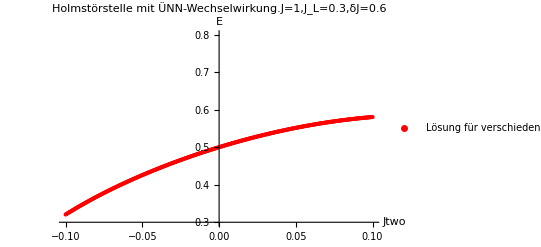

```mathematica
P = ListPlot[Fueger[moduler[Lister[1,0.0005,0.5]],moduler[Lister[-1,-0.0005,0.5]]],AxesLabel->{Jtwo,"E"},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.3,δJ=0.6",PlotRange->{0.3,0.8},PlotStyle->Red]
```

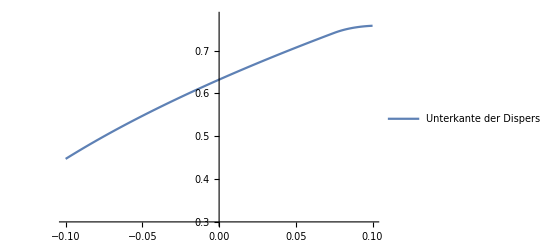

```mathematica
G = Plot[Sqrt[1+2*(0.3*Cos[Inv[0.3,Jtwo]]+Jtwo*Cos[2*Inv[0.3,Jtwo]])],{Jtwo,-0.1,0.1},PlotRange->{0.3,0.78},PlotLegends->{"Unterkante der Dispersion"}]
```

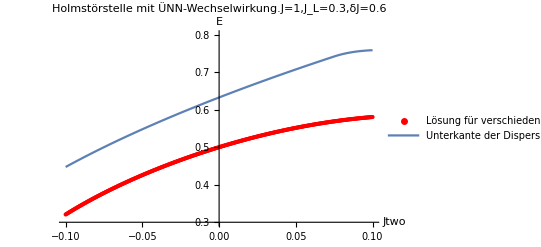

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.3,moduler[Lister[-1,-0.005,0.5]]]
```

{{-0.005,0.130862},{-0.01,0.129393},{-0.015,0.128046},{-0.02,0.126821},{-0.025,0.125719},{-0.03,0.12474},{-0.035,0.123885},{-0.04,0.123156},{-0.045,0.122555},{-0.05,0.122087},{-0.055,0.121755},{-0.06,0.121566},{-0.065,0.121527},{-0.07,0.121647},{-0.075,0.121938},{-0.08,0.122412},{-0.085,0.123088},{-0.09,0.123985},{-0.095,0.125131},{-0.1,0.126558}}

```mathematica
differ[1,0.3,moduler[Lister[1,0.005,0.5]]]
```

{{0.005,0.134174},{0.01,0.13602},{0.015,0.137994},{0.02,0.1401},{0.025,0.142339},{0.03,0.144716},{0.035,0.147232},{0.04,0.149892},{0.045,0.152698},{0.05,0.155655},{0.055,0.158765},{0.06,0.162033},{0.065,0.165461},{0.07,0.169055},{0.075,0.754073},{0.08,0.175915},{0.085,0.177737},{0.09,0.178554},{0.095,0.178575},{0.1,0.177963}}

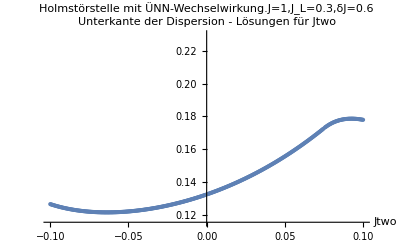

```mathematica
ListPlot[Fueger[differ[-1,0.3,moduler[Lister[-1,-0.0005,0.5]]],differ[1,0.3,moduler[Lister[1,0.0005,0.5]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.3,δJ=0.6"]
```

```mathematica
Fueger[moduler[Lister[1,0.0005,0.5]],moduler[Lister[-1,-0.0005,0.5]]]
```

{{0.0005,0.500624},{0.001,0.501246},{0.0015,0.501865},{0.002,0.502482},{0.0025,0.503097},{0.003,0.50371},{0.0035,0.50432},{0.004,0.504929},{0.0045,0.505535},{0.005,0.506138},{0.0055,0.50674},{0.006,0.507339},{0.0065,0.507936},{0.007,0.508531},{0.0075,0.509124},{0.008,0.509715},{0.0085,0.510303},{0.009,0.510889},{0.0095,0.511473},{0.01,0.512055},{0.0105,0.512634},{0.011,0.513211},{0.0115,0.513786},{0.012,0.514359},{0.0125,0.51493},{0.013,0.515498},{0.0135,0.516064},{0.014,0.516628},{0.0145,0.51719},{0.015,0.51775},{0.0155,0.518307},{0.016,0.518863},{0.0165,0.519416},{0.017,0.519966},{0.0175,0.520515},{0.018,0.521062},{0.0185,0.521606},{0.019,0.522148},{0.0195,0.522688},{0.02,0.523225},{0.0205,0.523761},{0.021,0.524294},{0.0215,0.524825},{0.022,0.525354},{0.0225,0.525881},{0.023,0.526405},{0.0235,0.526927},{0.024,0.527447},{0.0245,0.527965},{0.025,0.528481},{0.0255,0.528995},{0.026,0.529506},{0.0265,0.530015},{0.027,0.530522},{0.0275,0.531027},{0.028,0.531529},{0.0285,0.532029},{0.029,0.532527},{0.0295,0.533023},{0.03,0.533517},{0.0305,0.534009},{0.031,0.534498},{0.0315,0.534985},{0.032,0.53547},{0.0325,0.535953},{0.033,0.536433},{0.0335,0.536911},{0.034,0.537388},{0.0345,0.537861},{0.035,0.538333},{0.0355,0.538803},{0.036,0.53927},{0.0365,0.539735},{0.037,0.540198},{0.0375,0.540658},{0.038,0.541117},{0.0385,0.541573},{0.039,0.542027},{0.0395,0.542479},{0.04,0.542928},{0.0405,0.543376},{0.041,0.543821},{0.0415,0.544264},{0.042,0.544704},{0.0425,0.545143},{0.043,0.545579},{0.0435,0.546013},{0.044,0.546445},{0.0445,0.546874},{0.045,0.547302},{0.0455,0.547727},{0.046,0.54815},{0.0465,0.54857},{0.047,0.548989},{0.0475,0.549405},{0.048,0.549819},{0.0485,0.55023},{0.049,0.55064},{0.0495,0.551047},{0.05,0.551452},{0.0505,0.551855},{0.051,0.552255},{0.0515,0.552653},{0.052,0.553049},{0.0525,0.553443},{0.053,0.553835},{0.0535,0.554224},{0.054,0.554611},{0.0545,0.554995},{0.055,0.555378},{0.0555,0.555758},{0.056,0.556136},{0.0565,0.556512},{0.057,0.556885},{0.0575,0.557256},{0.058,0.557625},{0.0585,0.557992},{0.059,0.558356},{0.0595,0.558718},{0.06,0.559078},{0.0605,0.559435},{0.061,0.55979},{0.0615,0.560143},{0.062,0.560494},{0.0625,0.560842},{0.063,0.561188},{0.0635,0.561532},{0.064,0.561873},{0.0645,0.562213},{0.065,0.56255},{0.0655,0.562884},{0.066,0.563216},{0.0665,0.563546},{0.067,0.563874},{0.0675,0.5642},{0.068,0.564523},{0.0685,0.564843},{0.069,0.565162},{0.0695,0.565478},{0.07,0.565792},{0.0705,0.566103},{0.071,0.566413},{0.0715,0.56672},{0.072,0.567024},{0.0725,0.567326},{0.073,0.567626},{0.0735,0.567924},{0.074,0.568219},{0.0745,0.568512},{0.075,0.568803},{0.0755,0.569091},{0.076,0.569377},{0.0765,0.569661},{0.077,0.569942},{0.0775,0.570221},{0.078,0.570498},{0.0785,0.570772},{0.079,0.571044},{0.0795,0.571313},{0.08,0.571581},{0.0805,0.571845},{0.081,0.572108},{0.0815,0.572368},{0.082,0.572626},{0.0825,0.572881},{0.083,0.573134},{0.0835,0.573385},{0.084,0.573634},{0.0845,0.57388},{0.085,0.574123},{0.0855,0.574364},{0.086,0.574603},{0.0865,0.57484},{0.087,0.575074},{0.0875,0.575306},{0.088,0.575535},{0.0885,0.575762},{0.089,0.575987},{0.0895,0.576209},{0.09,0.576429},{0.0905,0.576647},{0.091,0.576862},{0.0915,0.577075},{0.092,0.577285},{0.0925,0.577493},{0.093,0.577698},{0.0935,0.577902},{0.094,0.578102},{0.0945,0.578301},{0.095,0.578497},{0.0955,0.57869},{0.096,0.578882},{0.0965,0.579071},{0.097,0.579257},{0.0975,0.579441},{0.098,0.579623},{0.0985,0.579802},{0.099,0.579979},{0.0995,0.580153},{0.1,0.580325},{-0.0005,0.499374},{-0.001,0.498746},{-0.0015,0.498115},{-0.002,0.497482},{-0.0025,0.496847},{-0.003,0.49621},{-0.0035,0.49557},{-0.004,0.494928},{-0.0045,0.494284},{-0.005,0.493638},{-0.0055,0.492989},{-0.006,0.492338},{-0.0065,0.491685},{-0.007,0.491029},{-0.0075,0.490372},{-0.008,0.489712},{-0.0085,0.489049},{-0.009,0.488385},{-0.0095,0.487718},{-0.01,0.487049},{-0.0105,0.486377},{-0.011,0.485704},{-0.0115,0.485028},{-0.012,0.484349},{-0.0125,0.483669},{-0.013,0.482986},{-0.0135,0.4823},{-0.014,0.481613},{-0.0145,0.480923},{-0.015,0.48023},{-0.0155,0.479536},{-0.016,0.478839},{-0.0165,0.47814},{-0.017,0.477438},{-0.0175,0.476734},{-0.018,0.476028},{-0.0185,0.475319},{-0.019,0.474608},{-0.0195,0.473894},{-0.02,0.473179},{-0.0205,0.47246},{-0.021,0.47174},{-0.0215,0.471017},{-0.022,0.470291},{-0.0225,0.469564},{-0.023,0.468833},{-0.0235,0.468101},{-0.024,0.467366},{-0.0245,0.466628},{-0.025,0.465889},{-0.0255,0.465146},{-0.026,0.464402},{-0.0265,0.463654},{-0.027,0.462905},{-0.0275,0.462153},{-0.028,0.461398},{-0.0285,0.460641},{-0.029,0.459881},{-0.0295,0.459119},{-0.03,0.458355},{-0.0305,0.457588},{-0.031,0.456818},{-0.0315,0.456046},{-0.032,0.455272},{-0.0325,0.454495},{-0.033,0.453715},{-0.0335,0.452933},{-0.034,0.452148},{-0.0345,0.451361},{-0.035,0.450571},{-0.0355,0.449779},{-0.036,0.448984},{-0.0365,0.448186},{-0.037,0.447386},{-0.0375,0.446583},{-0.038,0.445778},{-0.0385,0.44497},{-0.039,0.444159},{-0.0395,0.443346},{-0.04,0.44253},{-0.0405,0.441711},{-0.041,0.44089},{-0.0415,0.440065},{-0.042,0.439239},{-0.0425,0.438409},{-0.043,0.437577},{-0.0435,0.436742},{-0.044,0.435905},{-0.0445,0.435064},{-0.045,0.434221},{-0.0455,0.433375},{-0.046,0.432527},{-0.0465,0.431675},{-0.047,0.430821},{-0.0475,0.429964},{-0.048,0.429104},{-0.0485,0.428241},{-0.049,0.427376},{-0.0495,0.426507},{-0.05,0.425636},{-0.0505,0.424762},{-0.051,0.423884},{-0.0515,0.423004},{-0.052,0.422121},{-0.0525,0.421236},{-0.053,0.420347},{-0.0535,0.419455},{-0.054,0.41856},{-0.0545,0.417662},{-0.055,0.416761},{-0.0555,0.415858},{-0.056,0.414951},{-0.0565,0.414041},{-0.057,0.413128},{-0.0575,0.412212},{-0.058,0.411292},{-0.0585,0.41037},{-0.059,0.409445},{-0.0595,0.408516},{-0.06,0.407584},{-0.0605,0.406649},{-0.061,0.405711},{-0.0615,0.40477},{-0.062,0.403825},{-0.0625,0.402877},{-0.063,0.401926},{-0.0635,0.400972},{-0.064,0.400014},{-0.0645,0.399053},{-0.065,0.398088},{-0.0655,0.39712},{-0.066,0.396149},{-0.0665,0.395175},{-0.067,0.394196},{-0.0675,0.393215},{-0.068,0.39223},{-0.0685,0.391242},{-0.069,0.390249},{-0.0695,0.389254},{-0.07,0.388255},{-0.0705,0.387252},{-0.071,0.386246},{-0.0715,0.385236},{-0.072,0.384222},{-0.0725,0.383205},{-0.073,0.382184},{-0.0735,0.381159},{-0.074,0.380131},{-0.0745,0.379099},{-0.075,0.378062},{-0.0755,0.377023},{-0.076,0.375979},{-0.0765,0.374931},{-0.077,0.37388},{-0.0775,0.372824},{-0.078,0.371764},{-0.0785,0.370701},{-0.079,0.369633},{-0.0795,0.368562},{-0.08,0.367486},{-0.0805,0.366406},{-0.081,0.365322},{-0.0815,0.364234},{-0.082,0.363141},{-0.0825,0.362045},{-0.083,0.360943},{-0.0835,0.359838},{-0.084,0.358728},{-0.0845,0.357614},{-0.085,0.356496},{-0.0855,0.355372},{-0.086,0.354245},{-0.0865,0.353113},{-0.087,0.351976},{-0.0875,0.350834},{-0.088,0.349688},{-0.0885,0.348538},{-0.089,0.347382},{-0.0895,0.346222},{-0.09,0.345056},{-0.0905,0.343886},{-0.091,0.342711},{-0.0915,0.341531},{-0.092,0.340346},{-0.0925,0.339156},{-0.093,0.33796},{-0.0935,0.33676},{-0.094,0.335554},{-0.0945,0.334343},{-0.095,0.333126},{-0.0955,0.331905},{-0.096,0.330677},{-0.0965,0.329444},{-0.097,0.328206},{-0.0975,0.326962},{-0.098,0.325712},{-0.0985,0.324457},{-0.099,0.323196},{-0.0995,0.321928},{-0.1,0.320655}}

```mathematica
Fueger[differ[-1,0.3,moduler[Lister[-1,-0.0005,0.5]]],differ[1,0.3,moduler[Lister[1,0.0005,0.5]]]]
```

{{-0.0005,0.132291},{-0.001,0.132127},{-0.0015,0.131964},{-0.002,0.131803},{-0.0025,0.131643},{-0.003,0.131485},{-0.0035,0.131327},{-0.004,0.131171},{-0.0045,0.131016},{-0.005,0.130862},{-0.0055,0.13071},{-0.006,0.130558},{-0.0065,0.130408},{-0.007,0.13026},{-0.0075,0.130112},{-0.008,0.129966},{-0.0085,0.129821},{-0.009,0.129677},{-0.0095,0.129534},{-0.01,0.129393},{-0.0105,0.129252},{-0.011,0.129113},{-0.0115,0.128976},{-0.012,0.128839},{-0.0125,0.128704},{-0.013,0.12857},{-0.0135,0.128437},{-0.014,0.128305},{-0.0145,0.128175},{-0.015,0.128046},{-0.0155,0.127918},{-0.016,0.127791},{-0.0165,0.127666},{-0.017,0.127541},{-0.0175,0.127418},{-0.018,0.127297},{-0.0185,0.127176},{-0.019,0.127057},{-0.0195,0.126938},{-0.02,0.126821},{-0.0205,0.126706},{-0.021,0.126591},{-0.0215,0.126478},{-0.022,0.126366},{-0.0225,0.126255},{-0.023,0.126146},{-0.0235,0.126037},{-0.024,0.12593},{-0.0245,0.125824},{-0.025,0.125719},{-0.0255,0.125616},{-0.026,0.125514},{-0.0265,0.125413},{-0.027,0.125313},{-0.0275,0.125214},{-0.028,0.125117},{-0.0285,0.125021},{-0.029,0.124926},{-0.0295,0.124833},{-0.03,0.12474},{-0.0305,0.124649},{-0.031,0.124559},{-0.0315,0.124471},{-0.032,0.124383},{-0.0325,0.124297},{-0.033,0.124212},{-0.0335,0.124129},{-0.034,0.124046},{-0.0345,0.123965},{-0.035,0.123885},{-0.0355,0.123806},{-0.036,0.123729},{-0.0365,0.123653},{-0.037,0.123578},{-0.0375,0.123505},{-0.038,0.123432},{-0.0385,0.123361},{-0.039,0.123292},{-0.0395,0.123223},{-0.04,0.123156},{-0.0405,0.12309},{-0.041,0.123025},{-0.0415,0.122962},{-0.042,0.1229},{-0.0425,0.122839},{-0.043,0.12278},{-0.0435,0.122722},{-0.044,0.122665},{-0.0445,0.122609},{-0.045,0.122555},{-0.0455,0.122502},{-0.046,0.122451},{-0.0465,0.122401},{-0.047,0.122352},{-0.0475,0.122304},{-0.048,0.122258},{-0.0485,0.122213},{-0.049,0.12217},{-0.0495,0.122128},{-0.05,0.122087},{-0.0505,0.122047},{-0.051,0.122009},{-0.0515,0.121973},{-0.052,0.121937},{-0.0525,0.121903},{-0.053,0.121871},{-0.0535,0.12184},{-0.054,0.12181},{-0.0545,0.121782},{-0.055,0.121755},{-0.0555,0.12173},{-0.056,0.121706},{-0.0565,0.121683},{-0.057,0.121662},{-0.0575,0.121642},{-0.058,0.121624},{-0.0585,0.121607},{-0.059,0.121592},{-0.0595,0.121578},{-0.06,0.121566},{-0.0605,0.121555},{-0.061,0.121546},{-0.0615,0.121538},{-0.062,0.121532},{-0.0625,0.121527},{-0.063,0.121524},{-0.0635,0.121522},{-0.064,0.121522},{-0.0645,0.121524},{-0.065,0.121527},{-0.0655,0.121532},{-0.066,0.121538},{-0.0665,0.121546},{-0.067,0.121555},{-0.0675,0.121567},{-0.068,0.121579},{-0.0685,0.121594},{-0.069,0.12161},{-0.0695,0.121628},{-0.07,0.121647},{-0.0705,0.121668},{-0.071,0.121691},{-0.0715,0.121716},{-0.072,0.121742},{-0.0725,0.12177},{-0.073,0.1218},{-0.0735,0.121832},{-0.074,0.121865},{-0.0745,0.1219},{-0.075,0.121938},{-0.0755,0.121976},{-0.076,0.122017},{-0.0765,0.12206},{-0.077,0.122104},{-0.0775,0.122151},{-0.078,0.122199},{-0.0785,0.122249},{-0.079,0.122302},{-0.0795,0.122356},{-0.08,0.122412},{-0.0805,0.12247},{-0.081,0.12253},{-0.0815,0.122593},{-0.082,0.122657},{-0.0825,0.122723},{-0.083,0.122792},{-0.0835,0.122863},{-0.084,0.122935},{-0.0845,0.12301},{-0.085,0.123088},{-0.0855,0.123167},{-0.086,0.123249},{-0.0865,0.123333},{-0.087,0.123419},{-0.0875,0.123507},{-0.088,0.123598},{-0.0885,0.123691},{-0.089,0.123787},{-0.0895,0.123885},{-0.09,0.123985},{-0.0905,0.124088},{-0.091,0.124194},{-0.0915,0.124302},{-0.092,0.124412},{-0.0925,0.124525},{-0.093,0.124641},{-0.0935,0.12476},{-0.094,0.124881},{-0.0945,0.125005},{-0.095,0.125131},{-0.0955,0.125261},{-0.096,0.125393},{-0.0965,0.125528},{-0.097,0.125666},{-0.0975,0.125807},{-0.098,0.125951},{-0.0985,0.126098},{-0.099,0.126249},{-0.0995,0.126402},{-0.1,0.126558},{0.0005,0.132622},{0.001,0.132789},{0.0015,0.132958},{0.002,0.133128},{0.0025,0.133299},{0.003,0.133472},{0.0035,0.133645},{0.004,0.13382},{0.0045,0.133997},{0.005,0.134174},{0.0055,0.134353},{0.006,0.134533},{0.0065,0.134714},{0.007,0.134897},{0.0075,0.135081},{0.008,0.135266},{0.0085,0.135452},{0.009,0.13564},{0.0095,0.135829},{0.01,0.13602},{0.0105,0.136211},{0.011,0.136404},{0.0115,0.136598},{0.012,0.136794},{0.0125,0.13699},{0.013,0.137189},{0.0135,0.137388},{0.014,0.137589},{0.0145,0.137791},{0.015,0.137994},{0.0155,0.138199},{0.016,0.138404},{0.0165,0.138612},{0.017,0.13882},{0.0175,0.13903},{0.018,0.139241},{0.0185,0.139454},{0.019,0.139668},{0.0195,0.139883},{0.02,0.1401},{0.0205,0.140318},{0.021,0.140537},{0.0215,0.140757},{0.022,0.140979},{0.0225,0.141203},{0.023,0.141427},{0.0235,0.141653},{0.024,0.141881},{0.0245,0.142109},{0.025,0.142339},{0.0255,0.142571},{0.026,0.142804},{0.0265,0.143038},{0.027,0.143273},{0.0275,0.14351},{0.028,0.143749},{0.0285,0.143988},{0.029,0.14423},{0.0295,0.144472},{0.03,0.144716},{0.0305,0.144961},{0.031,0.145208},{0.0315,0.145456},{0.032,0.145706},{0.0325,0.145956},{0.033,0.146209},{0.0335,0.146463},{0.034,0.146718},{0.0345,0.146974},{0.035,0.147232},{0.0355,0.147492},{0.036,0.147753},{0.0365,0.148015},{0.037,0.148279},{0.0375,0.148544},{0.038,0.148811},{0.0385,0.149079},{0.039,0.149349},{0.0395,0.14962},{0.04,0.149892},{0.0405,0.150166},{0.041,0.150441},{0.0415,0.150718},{0.042,0.150997},{0.0425,0.151277},{0.043,0.151558},{0.0435,0.151841},{0.044,0.152125},{0.0445,0.152411},{0.045,0.152698},{0.0455,0.152987},{0.046,0.153278},{0.0465,0.153569},{0.047,0.153863},{0.0475,0.154158},{0.048,0.154454},{0.0485,0.154752},{0.049,0.155051},{0.0495,0.155352},{0.05,0.155655},{0.0505,0.155959},{0.051,0.156264},{0.0515,0.156572},{0.052,0.15688},{0.0525,0.15719},{0.053,0.157502},{0.0535,0.157816},{0.054,0.15813},{0.0545,0.158447},{0.055,0.158765},{0.0555,0.159085},{0.056,0.159406},{0.0565,0.159729},{0.057,0.160053},{0.0575,0.160379},{0.058,0.160706},{0.0585,0.161036},{0.059,0.161366},{0.0595,0.161699},{0.06,0.162033},{0.0605,0.162368},{0.061,0.162705},{0.0615,0.163044},{0.062,0.163385},{0.0625,0.163727},{0.063,0.16407},{0.0635,0.164416},{0.064,0.164763},{0.0645,0.165111},{0.065,0.165461},{0.0655,0.165813},{0.066,0.166167},{0.0665,0.166522},{0.067,0.166879},{0.0675,0.167237},{0.068,0.167598},{0.0685,0.167959},{0.069,0.168323},{0.0695,0.168688},{0.07,0.169055},{0.0705,0.169424},{0.071,0.169794},{0.0715,0.170166},{0.072,0.170539},{0.0725,0.170915},{0.073,0.171292},{0.0735,0.17167},{0.074,0.172051},{0.0745,0.172433},{0.075,0.754073},{0.0755,0.173194},{0.076,0.173554},{0.0765,0.1739},{0.077,0.17423},{0.0775,0.174546},{0.078,0.174847},{0.0785,0.175134},{0.079,0.175408},{0.0795,0.175668},{0.08,0.175915},{0.0805,0.17615},{0.081,0.176372},{0.0815,0.176582},{0.082,0.17678},{0.0825,0.176967},{0.083,0.177143},{0.0835,0.177307},{0.084,0.177461},{0.0845,0.177604},{0.085,0.177737},{0.0855,0.17786},{0.086,0.177974},{0.0865,0.178077},{0.087,0.178172},{0.0875,0.178257},{0.088,0.178334},{0.0885,0.178401},{0.089,0.17846},{0.0895,0.178511},{0.09,0.178554},{0.0905,0.178589},{0.091,0.178616},{0.0915,0.178636},{0.092,0.178648},{0.0925,0.178653},{0.093,0.178651},{0.0935,0.178642},{0.094,0.178626},{0.0945,0.178604},{0.095,0.178575},{0.0955,0.17854},{0.096,0.178499},{0.0965,0.178451},{0.097,0.178398},{0.0975,0.178339},{0.098,0.178275},{0.0985,0.178205},{0.099,0.178129},{0.0995,0.178048},{0.1,0.177963}}